## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PYK1";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "PYK1_5";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

True

Working dir:/home/mrama/Dropbox/MASSef/examples/PYK/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(adp^c+pep^c⇌atp^c+pyr^c)^PYK1

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | Null | 22000 | 20900.
23100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.0003 | 0.00028
0.00032 | fdp | 0.002
pep | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.00363 | 0.00359
0.00367 | adp | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00008 | 0.00007
0.00009 | fdp | 0.002
adp | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | 0.002 | 369.346 | 345.323
393.368 | 1/s | 7.5 | 37 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | Null
adp | 0.002
fdp | 0.002 | 480.45 | 456.427
504.472 | 1/s | 7.5 | 37 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.002
adp | Null
fdp | 0.002 | 396.371 | 375.351
417.391 | 1/s | 7.5 | 37 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | pep | 3.2 | 3.14
3.26 | adp | 0.002 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1 | 0.98
1.02 | fdp | 0.002
adp | 0.002 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

### Define data points priority (optional)

```mathematica
otherParmsList0[[1,4]] = 1.5
```

1.5

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {0};
s05Priorities = {1,0};
kcatPriorities = {1,0,0};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities ={1,0};


{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(adp^c+pep^c⇌atp^c+pyr^c)^PYK1

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | Null | 22000 | 20900.
23100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.00363 | 0.00359
0.00367 | adp | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | 0.002 | 369.346 | 345.323
393.368 | 1/s | 7.5 | 37 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | pep | 3.2 | 3.14
3.26 | adp | 0.002 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
enz ="E_PYK1[c]";
substrateList ={"pep", "adp"};
productList={"pyr", "atp"};
nActiveSites = 4;
bindingReversibility = " <=> ";
releaseReversibility = " <=> ";
transitionReversibility = " <=> ";


catalyticBranch=generateOrderedMechanism[enz, substrateList,  productList, nActiveSites, bindingReversibility, 
						transitionReversibility, releaseReversibility] ;



catalyticBranch=Union[catalyticBranch,{ "E_PYK1[c] <=>E_PYK1T[c]"}];
```

```mathematica
enzymeModelOrig=constructEnzymeModule[ID-> "PYK1",Mechanism->catalyticBranch,Activators->{},ActivationSites->1,Inhibitors->{},InhibitionSites->1];

catalyticBranch//TableForm
enzymeModelOrig["Reactions"]
```

E_PYK1[c] <=>E_PYK1T[c]
E_PYK1[c] + pep[c] <=> E_PYK1[c]&pep
E_PYK1[c]&pep + pep[c] <=> E_PYK1[c]&pep&pep
E_PYK1[c]&pep&pep + pep[c] <=> E_PYK1[c]&pep&pep&pep
E_PYK1[c]&pep&pep&pep&pep&adp&adp&adp + adp[c] <=> E_PYK1[c]&pep&pep&pep&pep&adp&adp&adp&adp
E_PYK1[c]&pep&pep&pep&pep&adp&adp&adp&adp <=> E_PYK1[c]&pyr&pyr&pyr&pyr&atp&atp&atp&atp
E_PYK1[c]&pep&pep&pep&pep&adp&adp + adp[c] <=> E_PYK1[c]&pep&pep&pep&pep&adp&adp&adp
E_PYK1[c]&pep&pep&pep&pep&adp + adp[c] <=> E_PYK1[c]&pep&pep&pep&pep&adp&adp
E_PYK1[c]&pep&pep&pep&pep + adp[c] <=> E_PYK1[c]&pep&pep&pep&pep&adp
E_PYK1[c]&pep&pep&pep + pep[c] <=> E_PYK1[c]&pep&pep&pep&pep
E_PYK1[c]&pyr <=> E_PYK1[c] + pyr[c]
E_PYK1[c]&pyr&pyr <=> E_PYK1[c]&pyr + pyr[c]
E_PYK1[c]&pyr&pyr&pyr <=> E_PYK1[c]&pyr&pyr + pyr[c]
E_PYK1[c]&pyr&pyr&pyr&pyr&atp&atp&atp&atp <=> E_PYK1[c]&pyr&pyr&pyr&pyr&atp&atp&atp + atp[c]
E_PYK1[c]&pyr&pyr&pyr&pyr&atp&atp&atp <=> E_PYK1[c]&pyr&pyr&pyr&pyr&atp&atp + atp[c]
E_PYK1[c]&pyr&pyr&pyr&pyr&atp&atp <=> E_PYK1[c]&pyr&pyr&pyr&pyr&atp + atp[c]
E_PYK1[c]&pyr&pyr&pyr&pyr&atp <=> E_PYK1[c]&pyr&pyr&pyr&pyr + atp[c]
E_PYK1[c]&pyr&pyr&pyr&pyr <=> E_PYK1[c]&pyr&pyr&pyr + pyr[c]

{((PYK1^c)_^+pep^c⇌(PYK1^c&pep^c)_^)^PYK11,((PYK1^c)_^⇌(PYK1T^c)_^)^PYK12,((PYK1^c&pyr^c)_^⇌(PYK1^c)_^+pyr^c)^PYK13,((PYK1^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c)_^)^PYK14,((PYK1^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c)_^+pyr^c)^PYK15,((PYK1^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c)_^)^PYK16,((PYK1^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c)_^+pyr^c)^PYK17,((PYK1^c&pep^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c)_^)^PYK18,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c)_^+pyr^c)^PYK19,((PYK1^c&pep^c&pep^c&pep^c&pep^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^)^PYK110,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^+atp^c)^PYK111,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^)^PYK112,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^+atp^c)^PYK113,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^)^PYK114,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^+atp^c)^PYK115,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^)^PYK116,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^+atp^c)^PYK117,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^)^PYK118}

### Define all catalytic tracks

```mathematica
catalyticReactionsSetsList = {{((PYK1^c)_^+pep^c⇌(PYK1^c&pep^c)_^)^PYK11,Overscript[(PYK1^c&pyr^c)_^⇌(PYK1^c)_^+pyr^c, PYK12],((PYK1^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c)_^)^PYK13,Overscript[(PYK1^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c)_^+pyr^c, PYK14],((PYK1^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c)_^)^PYK15,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c)_^+pyr^c, PYK16],((PYK1^c&pep^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c)_^)^PYK17,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c)_^+pyr^c, PYK18],((PYK1^c&pep^c&pep^c&pep^c&pep^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^)^PYK19,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^+atp^c, PYK110],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^)^PYK111,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^+atp^c, PYK112],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^)^PYK113,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^+atp^c, PYK114],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^)^PYK115,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^+atp^c, PYK116],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^)^PYK117}};
```

```mathematica
getEquivalentRateConsts2[enzymeModel_]:=Block[{metList, enzFormList, res,res1, res2, res3, res4, res5, boundMets, rateConstSub, boundEnz, enzList, transitionID},

metList = Cases[enzymeModel["Species"], _metabolite];
enzFormList=Cases[enzymeModel["Species"], _enzyme];
enzList = Map[getID@#&,enzFormList]//DeleteDuplicates;

	res = Table[
			Table[		
					Table[
					
							Which[Length[Cases[getSubstrates[rxn],_metabolite]] > 0 &&SameQ[Cases[getSubstrates[rxn],_metabolite][[1]], met]  && SameQ[getID@Cases[getSubstrates[rxn],_enzyme][[1]], enz] ,
								rxn,
		
								Length[Cases[getProducts[rxn],_metabolite]] > 0 &&SameQ[Cases[getProducts[rxn],_metabolite][[1]], met]&& SameQ[getID@Cases[getSubstrates[rxn],_enzyme][[1]], enz],
							rxn					
							],

							{rxn, enzymeModel["Reactions"]}],
	
					{met, metList}],
			{enz,enzList}];

res1 = Table[
		Table[
		If[ Length[getSubstrates@rxn1] == 1 && Length[getSubstrates@rxn2] == 1 && 
		Length[getProducts@rxn1] == 1 && Length[getProducts@rxn2] == 1 && 
	SameQ[DeleteDuplicates@getCatalytic[getSubstrates[rxn1][[1]]], DeleteDuplicates@getCatalytic[getSubstrates[rxn2][[1]]]] &&
	SameQ[DeleteDuplicates@getCatalytic[getProducts[rxn1][[1]]], DeleteDuplicates@getCatalytic[getProducts[rxn2][[1]]]] &&
SameQ[getID[getSubstrates[rxn1][[1]]], getID[getSubstrates[rxn2][[1]]]],
			rxn1

],
{rxn1, enzymeModel["Reactions"]}],

{rxn2, enzymeModel["Reactions"]}];


AppendTo[res, res1];

res2 = Map[Flatten@DeleteCases[#, Null]&, Flatten[res,1]];

	res3 =Table[ 
		Table[
					
					boundMets=DeleteDuplicates@getCatalytic[enzForm];
					boundEnz = getID[enzForm ];

						Table[
					
						Which[SameQ[DeleteDuplicates@getCatalytic[Cases[getSubstrates[rxn],_enzyme][[1]]], boundMets] ,
					
							{rateconst[getID[rxn], True], rateconst[getID[rxn], False]},
		
							SameQ[DeleteDuplicates@getCatalytic[Cases[getProducts[rxn],_enzyme][[1]]], boundMets]  ,
					
							{rateconst[getID[rxn], True], rateconst[getID[rxn], False]}
						],

						{rxn, rxnGroup}],
	
				{enzForm, enzFormList}],
{rxnGroup, res2}];

res4 = DeleteDuplicates@ DeleteCases[Map[Flatten@DeleteCases[#, Null]&,Flatten[res3,1]],{}];

res5=Table[
If[Length[entry]>2,
	entry],
{entry, res4}];

rateConstSub=DeleteCases[res5, Null];


rateConstSub = Table[
					{Map[#-> ratesGroup[[1]]&, ratesGroup[[1;; Length@ratesGroup;; 2]]],
						Map[#-> ratesGroup[[2]]&, ratesGroup[[2;; Length@ratesGroup;; 2]]]},

					{ratesGroup, rateConstSub}] // Flatten;


Return[rateConstSub];

];
```

```mathematica
ratesSub =  getEquivalentRateConsts2[enzymeModelOrig];
```

```mathematica
DeleteDuplicates[Values@ratesSub]
```

{k_PYK110^⟶,k_PYK110^⟵,k_PYK111^⟶,k_PYK111^⟵,k_PYK11^⟶,k_PYK11^⟵,k_PYK13^⟶,k_PYK13^⟵}

```mathematica
catalyticReactionsSetsList
```

{{((FBP2R^c)_^+fdp^c⇌(FBP2R^c&fdp^c)_^)^FBP22,((FBP2R^c&pi^c)_^⇌(FBP2R^c)_^+pi^c)^FBP23,((FBP2R^c&fdp^c)_^+fdp^c⇌(FBP2R^c&fdp^c&fdp^c)_^)^FBP24,((FBP2R^c&pi^c&pi^c)_^⇌(FBP2R^c&pi^c)_^+pi^c)^FBP25,((FBP2R^c&fdp^c&fdp^c)_^⇌(FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^)^FBP26,((FBP2R^c&pi^c&pi^c&f6p^c)_^⇌(FBP2R^c&pi^c&pi^c)_^+f6p^c)^FBP27,((FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^⇌(FBP2R^c&pi^c&pi^c&f6p^c)_^+f6p^c)^FBP28}}

```mathematica
enzymeModelOrig["Reactions"]
```

{((FBP2T^c)_^⇌(FBP2R^c)_^)^FBP21,((FBP2R^c)_^+fdp^c⇌(FBP2R^c&fdp^c)_^)^FBP22,((FBP2R^c&pi^c)_^⇌(FBP2R^c)_^+pi^c)^FBP23,((FBP2R^c&fdp^c)_^+fdp^c⇌(FBP2R^c&fdp^c&fdp^c)_^)^FBP24,((FBP2R^c&pi^c&pi^c)_^⇌(FBP2R^c&pi^c)_^+pi^c)^FBP25,((FBP2R^c&fdp^c&fdp^c)_^⇌(FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^)^FBP26,((FBP2R^c&pi^c&pi^c&f6p^c)_^⇌(FBP2R^c&pi^c&pi^c)_^+f6p^c)^FBP27,((FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^⇌(FBP2R^c&pi^c&pi^c&f6p^c)_^+f6p^c)^FBP28}

## Set up rate equations

```mathematica
nActiveSites
```

4

```mathematica
MWCFlag=False;
equivalentReactionsSetsList={};
assumedSaturatingConc = 1;
nActiveSites = 1;
simplifyFlag=True;
simplifyMaxTime=30;
inhibitionListSubset=inhibitionList;
otherMetsForwardZeroSub={};otherMetsReverseZeroSub={};
```

```mathematica
Get["MASSef`"];
```

```mathematica
rxnMets =  Map[getID[#]&, Flatten[{getSubstrates[rxn], getProducts[rxn]}]];
	If[ !SameQ[inhibitionList, {}],
		inhibitors = inhibitionList[[All,3]];
		prodInhibBool = MemberQ[Map[MemberQ[rxnMets, #]&, inhibitors], True];,
		prodInhibBool = False;
	];

	{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn, assumedSaturatingConc];
	rates = getEnzymeRates[enzymeModelOrig];
	{KeqName, KeqVal, volumeSub} = getMisc[enzymeModelOrig, rxnName];
```

```mathematica
enzymeModelOrig["Reactions"]
```

```mathematica
{allCatalyticReactions, nonCatalyticReactions} = classifyReactions[enzymeModelOrig];
	

rateConstSubstitutionList = 
	If[TrueQ[MWCFlag],
		getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions],
		{}
	];
```

```mathematica
allCatalyticReactions
```

```mathematica
nonCatalyticReactions={((PYK1^c)_^⇌(PYK1T^c)_^)^PYK12};
```

```mathematica
allCatalyticReactions = {((PYK1^c)_^+pep^c⇌(PYK1^c&pep^c)_^)^PYK11,Overscript[(PYK1^c&pyr^c)_^⇌(PYK1^c)_^+pyr^c, PYK13],((PYK1^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c)_^)^PYK14,Overscript[(PYK1^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c)_^+pyr^c, PYK15],((PYK1^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c)_^)^PYK16,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c)_^+pyr^c, PYK17],((PYK1^c&pep^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c)_^)^PYK18,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c)_^+pyr^c, PYK19],((PYK1^c&pep^c&pep^c&pep^c&pep^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^)^PYK110,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^+atp^c, PYK111],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^)^PYK112,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^+atp^c, PYK113],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^)^PYK114,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^+atp^c, PYK115],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^)^PYK116,Overscript[(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^+atp^c, PYK117],((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^)^PYK118};
```

```mathematica
If[ !SameQ[equivalentReactionsSetsList, {}] && !SameQ[equivalentReactionsSetsList, Null],
			AppendTo[rateConstSubstitutionList, getHalfHaldaneSub[equivalentReactionsSetsList]];
			rateConstSubstitutionList = Flatten @ rateConstSubstitutionList;
	];
```

```mathematica
(*Identify Transition Rate Equations*)
transitionID = getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs = getTransitionRateEqs[transitionID, rates];
```

```mathematica
transitionRateEqs
```

{((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^-((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^)/K_PYK118) Volume_c k_PYK118^⟶}

```mathematica
(*King-Altman Workaround UsingMathematicaSolve*)
	(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFluxNoProdInhib=
	If[prodInhibBool,
			Print["prod inhib"];
			getFluxEquation[inputPath, rxnName, enzymeModelOrig, rateConstSubstitutionList, transitionRateEqs, simplifyFlag, simplifyMaxTime,nActiveSites, "NoProdInhibRefactor"],
			Null
	];
```

```mathematica
If[!SameQ[inhibitionListSubset,{}],
		{enzymeModelOrig,nonCatalyticReactions} = addInhibitionReactions[enzymeModelOrig,rxnName,inhibitionListSubset,allCatalyticReactions,nonCatalyticReactions];
];
```

```mathematica
rateConstSubstitutionList = ratesSub;
rateConstSubstitutionList
```

{k_PYK110^⟶→k_PYK110^⟶,k_PYK112^⟶→k_PYK110^⟶,k_PYK114^⟶→k_PYK110^⟶,k_PYK116^⟶→k_PYK110^⟶,k_PYK110^⟵→k_PYK110^⟵,k_PYK112^⟵→k_PYK110^⟵,k_PYK114^⟵→k_PYK110^⟵,k_PYK116^⟵→k_PYK110^⟵,k_PYK111^⟶→k_PYK111^⟶,k_PYK113^⟶→k_PYK111^⟶,k_PYK115^⟶→k_PYK111^⟶,k_PYK117^⟶→k_PYK111^⟶,k_PYK111^⟵→k_PYK111^⟵,k_PYK113^⟵→k_PYK111^⟵,k_PYK115^⟵→k_PYK111^⟵,k_PYK117^⟵→k_PYK111^⟵,k_PYK11^⟶→k_PYK11^⟶,k_PYK14^⟶→k_PYK11^⟶,k_PYK16^⟶→k_PYK11^⟶,k_PYK18^⟶→k_PYK11^⟶,k_PYK11^⟵→k_PYK11^⟵,k_PYK14^⟵→k_PYK11^⟵,k_PYK16^⟵→k_PYK11^⟵,k_PYK18^⟵→k_PYK11^⟵,k_PYK13^⟶→k_PYK13^⟶,k_PYK15^⟶→k_PYK13^⟶,k_PYK17^⟶→k_PYK13^⟶,k_PYK19^⟶→k_PYK13^⟶,k_PYK13^⟵→k_PYK13^⟵,k_PYK15^⟵→k_PYK13^⟵,k_PYK17^⟵→k_PYK13^⟵,k_PYK19^⟵→k_PYK13^⟵}

### Get absolute flux based on KA patters

```mathematica
kineticMatrixLocal[model_MASSmodel,rateConstSubstitutionList_]:=Module[{enzPos,enzForms,ssEquations},
	enzPos=Flatten[Position[model["Species"],_enzyme]];
	enzForms=model["Species"][[enzPos]];
	ssEquations=model["ODE"][[enzPos]][[All,2]]/.elem_[t]:>elem;
	ssEquations = keq2kHT[ssEquations]/.rateConstSubstitutionList;
	{enzForms,Normal[CoefficientArrays[ssEquations,enzForms]][[2]]}
];
```

```mathematica
KingAltmanPatternsLocal[model_MASSmodel, rxnName_,rateConstSubstitutionList_]:=Module[{kMat,distributionTerms,kJJ,enzForms},
	{enzForms,kMat}=kineticMatrixLocal[model,rateConstSubstitutionList];
	distributionTerms=Table[
							(*kMatJ=ReplacePart[kMat,{_,i}->1];*)
							kJJ=kMat[[#,#]]&[Drop[Range[1,Length[kMat]],{i}]];
							enzForms[[i]]->anonymize[Det[kJJ]],
						{i,1,Length[enzForms]}];
			
			Table[
					enzForms[[i]]->(distributionTerms[[i,2]]/(Plus@@distributionTerms[[All,2]]))*parameter[rxnName <> "_total"],
			{i,1,Length[distributionTerms]}]
];
```

```mathematica
enzSol = KingAltmanPatternsLocal[enzymeModelOrig, rxnName,rateConstSubstitutionList];
```

```mathematica
enzSolSub = keq2kHT[enzSol/.volumeSub/.rateConstSubstitutionList];
```

```mathematica
fluxEq = Total[keq2kHT@transitionRateEqs]/.rateConstSubstitutionList(*]*);(*Flux Will Always Go through the Transition Step*)
fluxEq = fluxEq/.volumeSub;
fluxEq = Simplify[fluxEq];
```

```mathematica
fluxEqSub =fluxEq/.enzSolSub;
```

```mathematica
absoluteFlux = parameter["v", rxnName] -> nActiveSites * keq2kHT[anonymize[Simplify[fluxEqSub, TimeConstraint -> {30, 300}]]];
```

```mathematica
enSolFilePath = FileNameJoin[{inputPath, "enzSol_" <> rxnName<> "_" <> ""<> ".m"}, OperatingSystem->$OperatingSystem];
absFluxFilePath = FileNameJoin[{inputPath, "absoluteFlux_" <> rxnName<> "_" <> ""<> ".m"}, OperatingSystem->$OperatingSystem];
Export[enSolFilePath,  enzSolSub]; 
Export[absFluxFilePath, absoluteFlux];
```

### Get absolute flux from first principles

```mathematica
absoluteFlux = getFluxEquation[inputPath, rxnName, enzymeModelOrig, rateConstSubstitutionList, transitionRateEqs, True, simplifyMaxTime, nActiveSites, ""];
```

Generating flux equation...

{((FBP2R^c&fdp^c)_^-((FBP2R^c&pi^c&f6p^c)_^)/K_FBP25) Volume_c k_FBP25^⟶,((FBP2R^c&fdp^c&fdp^c)_^-((FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^)/K_FBP28) Volume_c k_FBP28^⟶}

Volume_c (-(FBP2R^c&pi^c&f6p^c)_^ k_FBP25^⟵-(FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^ k_FBP25^⟵+((FBP2R^c&fdp^c)_^+(FBP2R^c&fdp^c&fdp^c)_^) k_FBP25^⟶)

Simplifying...

```mathematica
Get["MASSef`"];
```

```mathematica
simplifyMaxTime=30;
```

```mathematica
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse} = 
		getRateEqs[rxn, enzymeModelOrig, absoluteFlux, rateConstSubstitutionList, reverseZeroSub, forwardZeroSub, volumeSub,
				metSatForSub, metSatRevSub, inputPath, Null, Null,
				otherMetsForwardZeroSub, otherMetsReverseZeroSub, simplifyFlag, simplifyMaxTime];
```

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

```mathematica
(* set up haldane relations *)
haldaneRatiosList  = Table[
				haldane = haldaneRelation[KeqName,catalyticReactionsSet]/.rateConstSubstitutionList;
				haldane[[2]],
		{catalyticReactionsSet, catalyticReactionsSetsList}] // DeleteDuplicates;
```

```mathematica
(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub} = 
			getMetRatesSubs[enzymeModelOrig, haldaneRatiosList, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
							relativeRateReverse,KeqVal,otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

```mathematica
(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub} = 
		exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
						relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub,
						otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

```mathematica
absoluteRateForward
```

Indeterminate

```mathematica
absoluteRateForward
```

((fdp^c)^2 FBP2_total_Global (k_FBP21^⟶)^2 k_FBP22^⟶ k_FBP25^⟶ k_FBP26^⟶)/((k_FBP21^⟵)^2 k_FBP22^⟶ (k_FBP25^⟵+k_FBP26^⟶)+k_FBP21^⟵ k_FBP22^⟶ (k_FBP25^⟶ k_FBP26^⟶+fdp^c k_FBP21^⟶ (k_FBP25^⟵+k_FBP26^⟶))+fdp^c k_FBP21^⟶ (2 k_FBP22^⟶ k_FBP25^⟶ k_FBP26^⟶+fdp^c k_FBP21^⟶ (2 k_FBP25^⟶ k_FBP26^⟶+k_FBP22^⟶ (k_FBP25^⟵+2 k_FBP25^⟶+k_FBP26^⟶))))

```mathematica
metsSub
```

{a^c→d<0>,b^c→d<1>,p^c→d<2>,q^c→d<3>,MWCtest_total_Global→d<4>,pH_Global→d<5>,Temp_Global→d<6>}

```mathematica
haldaneRatiosList
```

{((k_PYK11^⟶)^4 (k_PYK110^⟶)^4 (k_PYK111^⟶)^4 k_PYK12^⟶ (k_PYK13^⟶)^4)/((k_PYK11^⟵)^4 (k_PYK110^⟵)^4 (k_PYK111^⟵)^4 k_PYK12^⟵ (k_PYK13^⟵)^4)}

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

```mathematica
KeqList= {};
```

unifiedRateConstList

```mathematica
nonCatalyticReactions={}
```

{}

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModelOrig,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, rateConstSubstitutionList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	atp[c]	pep[c]	pyr[c]	param_PYK1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/haldaneRatio_1.txt"	22000
1	0.002	0	0.00036299999999999993	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.0006305594883398929
1	0.002	0	0.0005753162288633843	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.002746663763163244
1	0.002	0	0.0009118147746379772	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.011879817525171529
1	0.002	0	0.001445129029109195	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.04986385377897619
1	0.002	0	0.0022903751604631	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.18638778949441298
1	0.002	0	0.003629999999999999	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.49999999999999994
1	0.002	0	0.005753162288633843	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.8136122105055869
1	0.002	0	0.009118147746379781	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.9501361462210239
1	0.002	0	0.014451290291091951	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.9881201824748285
1	0.002	0	0.022903751604631012	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.9972533362368367
1	0.002	0	0.03629999999999999	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/relRateFor_pep.txt"	0.9993694405116601
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902
1	0.002	0	1	0	1	7.5	37	"/home/mrama/Dropbox/MASSef/examples/PYK/PYK1_5/input/absRateFor.txt"	369.3457634492902

```mathematica
haldaneRatiosList
```

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	6.681220703380521e-6	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.010008288260305101
1	0	0.000010589021210118044	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.024712420814393475
1	0	0.000016782467630742437	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.05971668328601667
1	0	0.000026598418700662637	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.13732197314049185
1	0	0.00004215565272891061	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.28519092739129753
1	0	0.0000668122070338052	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.49999999999999967
1	0	0.00010589021210118044	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.7148090726087021
1	0	0.00016782467630742438	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.8626780268595078
1	0	0.00026598418700662663	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9402833167139832
1	0	0.00042155652728910606	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9752875791856065
1	0	0.0006681220703380521	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9899917117396948
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479

### Parameter scan

```mathematica
paramScanList={{"s05",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModelOri, dataFileName, 
						 fitLabel,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, rateConstSubstitutionList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint[dataPathList[[8]]]
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	7.000000000000002e-6	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.00883377824981335
1	0	0.000011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.022395622457170455
1	0	0.00001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.055609816758203534
1	0	0.000027867501938744792	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.1314590000241482
1	0	0.000044167014113613516	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.28008099405284803
1	0	0.00007000000000000002	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.7199190059471522
1	0	0.0001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.8685409999758519
1	0	0.0002786750193874482	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9443901832417967
1	0	0.0004416701411361352	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9776043775428295
1	0	0.0007000000000000001	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9911662217501868
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=100;
numCPUs=1;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel,numCPUs];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.00967804435
best_fit: 4.38199525643
best_fit: 0.992227480224
best_fit: 0.890567973362
best_fit: 0.987173588436
best_fit: 0.489651690282
best_fit: 0.998073705367
best_fit: 1.09267553585
best_fit: 1.03757258156
best_fit: 0.917837850223
best_fit: 1.01543966494
best_fit: 0.893419965327
best_fit: 0.847198869609
best_fit: 0.385227517777
best_fit: 0.92484345796
best_fit: 1.0860952102
best_fit: 1.07734124303
best_fit: 0.633953414321
best_fit: 0.486415341079
best_fit: 1.0534721087
best_fit: 1.05928921838
best_fit: 0.432898488229
best_fit: 1.07609051938
best_fit: 1.0935146688
best_fit: 1.03271748294
best_fit: 0.53717045407
best_fit: 0.615679455853
best_fit: 0.448571383498
best_fit: 4.38199848195
best_fit: 0.512651688157
best_fit: 4.38204777817
best_fit: 0.64287797959
best_fit: 1.03940105286
best_fit: 1.09807293045
best_fit: 1.09052802423
best_fit: 1.18595455991
best_fit: 0.947791661553
best_fit: 1.08141235992
best_fit: 0.395284542296
best_fit: 1.09084892151
best_fit: 1.02266826218
best_fit: 0.833946496271
best_fit: 0.906080320795
best_fit: 0.693313702837
best_fit: 1.01095424962
best_fit: 0.945197061094
best_fit: 0.786508445931
best_fit: 1.08233516675
best_fit: 1.0857291101
best_fit: 0.749576867408
best_fit: 4.38201942356
best_fit: 1.06620890672
best_fit: 4.38190212146
best_fit: 4.38629010271
best_fit: 1.0908944188
best_fit: 0.947166997723
best_fit: 0.687767945067
best_fit: 0.193872642492
best_fit: 1.03717132399
best_fit: 1.04206421814
best_fit: 0.488685116428
best_fit: 0.792568741354
best_fit: 1.09188237023
best_fit: 4.38207085622
best_fit: 1.07278798386
best_fit: 0.380178299199
best_fit: 0.311882634373
best_fit: 0.951822639396
best_fit: 0.878502920637
best_fit: 0.823748053762
best_fit: 4.38204704943
best_fit: 1.02053990872
best_fit: 0.179249909094
best_fit: 0.2866558698
best_fit: 0.821609540984
best_fit: 1.09971590181
best_fit: 0.812799357893
best_fit: 0.684644923004
best_fit: 0.459643967362
best_fit: 4.39059547399
best_fit: 0.99837679629
best_fit: 0.828665285337
best_fit: 0.963601024805
best_fit: 0.55184221528
best_fit: 0.475513383274
best_fit: 1.04432905125
best_fit: 1.01921265109
best_fit: 0.561732617421
best_fit: 0.532340194618
best_fit: 0.85643058818
best_fit: 0.871134051411
best_fit: 1.0584392405
best_fit: 1.39227870594
best_fit: 1.00612881594
best_fit: 0.659334594255
best_fit: 0.719890314684
best_fit: 1.03099785108
best_fit: 0.975925095222
best_fit: 1.00449837718
best_fit: 0.572033598173

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 2.47772×10^-8 | 6.1391×10^-16 | 0.00125514 | 5.70516×10^-6 | 22000 | 22000.
1 | relRateFor_pep | 0.131239 | 0.0172236 | 0.000164451 | 26.0801 | 0.000630559 | 0.000466109
1 | relRateFor_pep | 0.0156339 | 0.00024442 | 0.0000971172 | 3.53583 | 0.00274666 | 0.00264955
1 | relRateFor_pep | 0.0697332 | 0.00486272 | 0.00206918 | 17.4176 | 0.0118798 | 0.013949
1 | relRateFor_pep | 0.101901 | 0.0103838 | 0.0131864 | 26.4447 | 0.0498639 | 0.0630502
1 | relRateFor_pep | 0.0555457 | 0.00308533 | 0.0254304 | 13.6438 | 0.186388 | 0.211818
1 | relRateFor_pep | 0.0355002 | 0.00126026 | 0.0392452 | 7.84905 | 0.5 | 0.460755
1 | relRateFor_pep | 0.0757302 | 0.00573507 | 0.130193 | 16.0018 | 0.813612 | 0.683419
1 | relRateFor_pep | 0.0638137 | 0.00407219 | 0.129837 | 13.6651 | 0.950136 | 0.820299
1 | relRateFor_pep | 0.0425054 | 0.00180671 | 0.0921277 | 9.32353 | 0.98812 | 0.895992
1 | relRateFor_pep | 0.0264265 | 0.000698358 | 0.0588727 | 5.90348 | 0.997253 | 0.938381
1 | relRateFor_pep | 0.0161161 | 0.000259729 | 0.0364057 | 3.64287 | 0.999369 | 0.962964
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346
1 | absRateFor | 7.96898×10^-7 | 6.35046×10^-13 | 0.000677722 | 0.000183493 | 369.346 | 369.346

### Simulated Data and Best Fit Data Plot

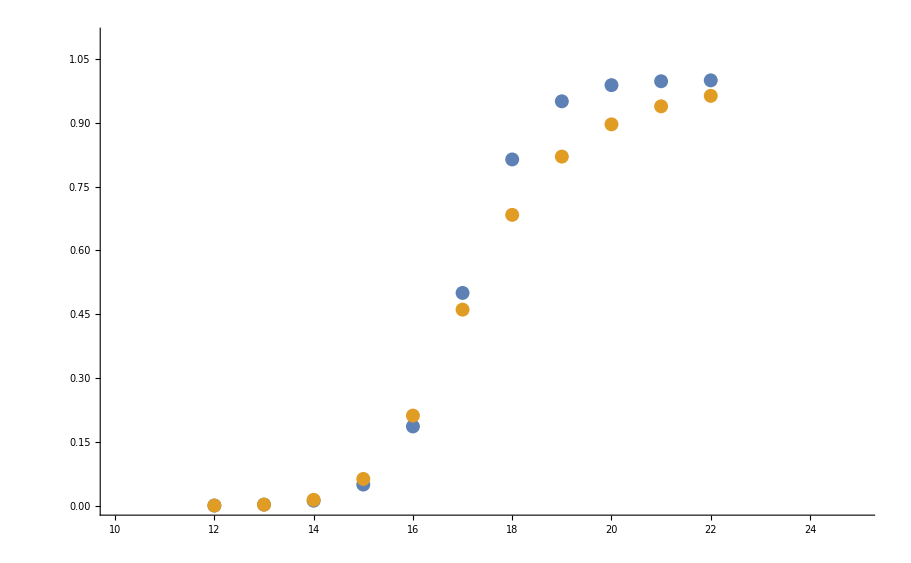

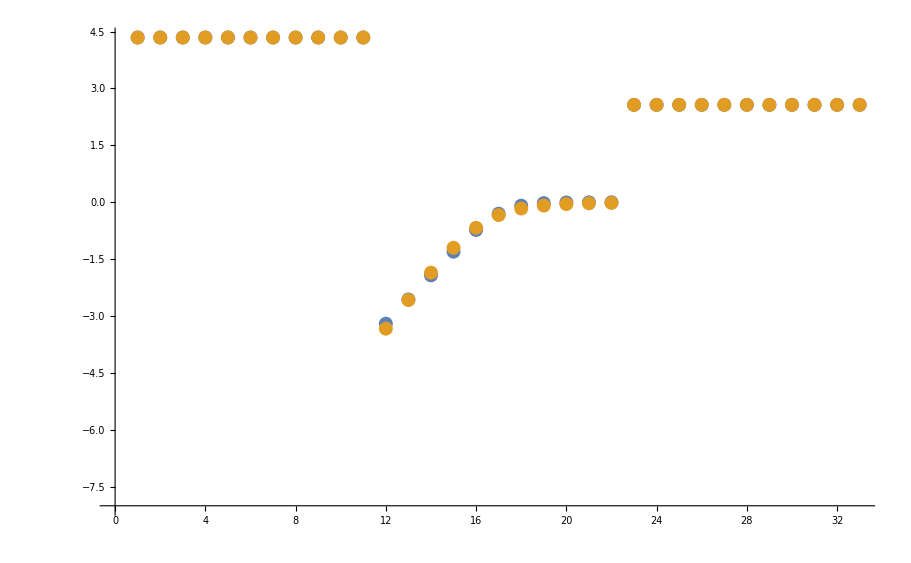

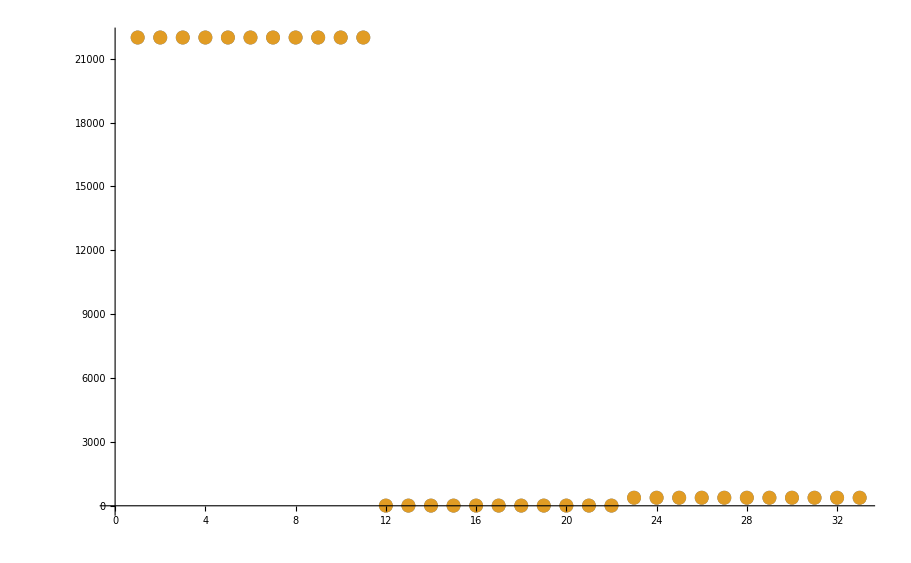

```mathematica
datasetI=1;
ListPlot[{fittingData[[All,-1]], filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}, PlotRange->{{10,25}, {0,1.1}}]
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

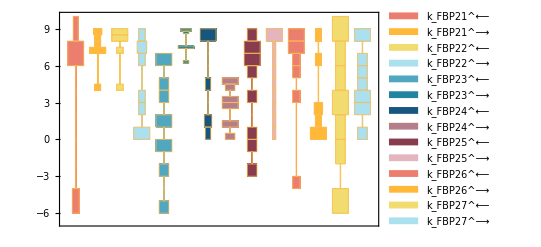

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

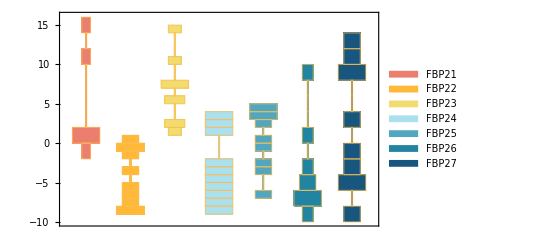

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

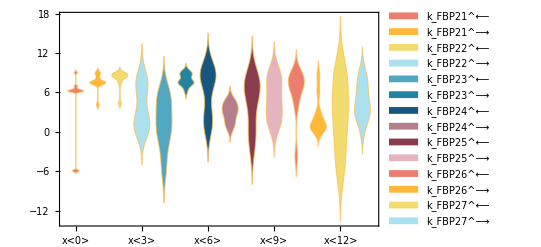

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

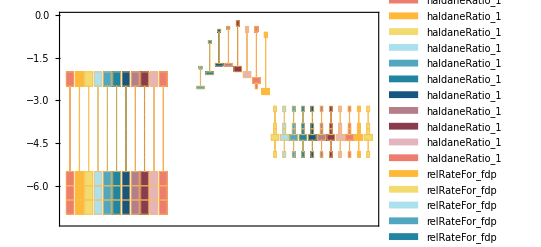

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
keq2kHT@enzymeModelOrig["Rates"]
```

{Volume_c k_FBP21^⟶ (-(k_FBP21^⟵ (FBP2R^c)_^[t])/k_FBP21^⟶+(FBP2T^c)_^[t]),Volume_c k_FBP22^⟶ (-(k_FBP22^⟵ (FBP2R^c&fdp^c)_^[t])/k_FBP22^⟶+(FBP2R^c)_^[t] fdp^c[t]),Volume_c k_FBP23^⟶ ((FBP2R^c&pi^c)_^[t]-(k_FBP23^⟵ (FBP2R^c)_^[t] pi^c[t])/k_FBP23^⟶),Volume_c k_FBP24^⟶ (-(k_FBP24^⟵ (FBP2R^c&fdp^c&fdp^c)_^[t])/k_FBP24^⟶+(FBP2R^c&fdp^c)_^[t] fdp^c[t]),Volume_c k_FBP25^⟶ ((FBP2R^c&pi^c&pi^c)_^[t]-(k_FBP25^⟵ (FBP2R^c&pi^c)_^[t] pi^c[t])/k_FBP25^⟶),Volume_c k_FBP26^⟶ ((FBP2R^c&fdp^c&fdp^c)_^[t]-(k_FBP26^⟵ (FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^[t])/k_FBP26^⟶),Volume_c k_FBP27^⟶ ((FBP2R^c&pi^c&pi^c&f6p^c)_^[t]-(k_FBP27^⟵ (FBP2R^c&pi^c&pi^c)_^[t] f6p^c[t])/k_FBP27^⟶),Volume_c k_FBP28^⟶ ((FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^[t]-(k_FBP28^⟵ (FBP2R^c&pi^c&pi^c&f6p^c)_^[t] f6p^c[t])/k_FBP28^⟶)}

```mathematica
(Subscript[k, FBP21]^⟶/Subscript[k, FBP21]^⟵)/.paramFitSub
```

1.08024×10^9

```mathematica
(Subscript[k, FBP22]^⟶/Subscript[k, FBP22]^⟵)/.paramFitSub
```

1.72093

```mathematica
(Subscript[k, FBP24]^⟶/Subscript[k, FBP24]^⟵)/.ratesSub/.paramFitSub
```

1.72093

#### Get total T/R ratio

```mathematica
enzymeModelOrig["Reactions"]
```

{((FBP2T^c)_^⇌(FBP2R^c)_^)^FBP21,((FBP2R^c)_^+fdp^c⇌(FBP2R^c&fdp^c)_^)^FBP22,((FBP2R^c&pi^c)_^⇌(FBP2R^c)_^+pi^c)^FBP23,((FBP2R^c&fdp^c)_^+fdp^c⇌(FBP2R^c&fdp^c&fdp^c)_^)^FBP24,((FBP2R^c&pi^c&pi^c)_^⇌(FBP2R^c&pi^c)_^+pi^c)^FBP25,((FBP2R^c&fdp^c&fdp^c)_^⇌(FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^)^FBP26,((FBP2R^c&pi^c&pi^c&f6p^c)_^⇌(FBP2R^c&pi^c&pi^c)_^+f6p^c)^FBP27,((FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^⇌(FBP2R^c&pi^c&pi^c&f6p^c)_^+f6p^c)^FBP28}

```mathematica
enzForms =Cases[keq2kHT@enzymeModelOrig["Species"], _enzyme]
```

{(FBP2R^c)_^,(FBP2R^c&fdp^c)_^,(FBP2R^c&pi^c)_^,(FBP2R^c&fdp^c&fdp^c)_^,(FBP2R^c&pi^c&pi^c)_^,(FBP2R^c&pi^c&pi^c&f6p^c)_^,(FBP2R^c&pi^c&pi^c&f6p^c&f6p^c)_^,(FBP2T^c)_^}

```mathematica
allEnzR = Select[enzForms, getID@#=="FBP2R"&];
allEnzR = Values@FilterRules[enzSolSub,allEnzR];
allEnzR = Simplify[Total[allEnzR/.ratesSub/.paramFitSub/.reverseZeroSub/.enzymeSub]];
Map[{ 10.^#,allEnzR/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,1.},{1.×10^-13,1.},{1.×10^-12,1.},{1.×10^-11,1.},{1.×10^-10,1.},{1.×10^-9,1.},{1.×10^-8,1.},{1.×10^-7,1.},{1.×10^-6,1.},{0.00001,1.},{0.0001,1.},{0.001,1.},{0.01,1.},{0.1,1.}}

```mathematica
allEnzT = Select[enzForms, getID@#=="FBP2T"&];
allEnzT = Values@FilterRules[enzSolSub,allEnzT];
allEnzT = Simplify[Total[allEnzT/.ratesSub/.paramFitSub/.reverseZeroSub/.enzymeSub]];
Map[{ 10.^#,allEnzT/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,9.25722×10^-10},{1.×10^-13,9.25722×10^-10},{1.×10^-12,9.25722×10^-10},{1.×10^-11,9.25722×10^-10},{1.×10^-10,9.25722×10^-10},{1.×10^-9,9.25722×10^-10},{1.×10^-8,9.25722×10^-10},{1.×10^-7,9.2572×10^-10},{1.×10^-6,9.25544×10^-10},{0.00001,9.0839×10^-10},{0.0001,3.18528×10^-10},{0.001,4.83599×10^-12},{0.01,4.90868×10^-14},{0.1,5.38411×10^-16}}

```mathematica
enzRatio=allEnzT/allEnzR;
Map[{ 10.^#,enzRatio/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,9.25722×10^-10},{1.×10^-13,9.25722×10^-10},{1.×10^-12,9.25722×10^-10},{1.×10^-11,9.25722×10^-10},{1.×10^-10,9.25722×10^-10},{1.×10^-9,9.25722×10^-10},{1.×10^-8,9.25722×10^-10},{1.×10^-7,9.2572×10^-10},{1.×10^-6,9.25544×10^-10},{0.00001,9.0839×10^-10},{0.0001,3.18528×10^-10},{0.001,4.83599×10^-12},{0.01,4.90868×10^-14},{0.1,5.38411×10^-16}}

```mathematica
enzSum=allEnzT+allEnzR;
Map[{ 10.^#,enzSum/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,1.},{1.×10^-13,1.},{1.×10^-12,1.},{1.×10^-11,1.},{1.×10^-10,1.},{1.×10^-9,1.},{1.×10^-8,1.},{1.×10^-7,1.},{1.×10^-6,1.},{0.00001,1.},{0.0001,1.},{0.001,1.},{0.01,1.},{0.1,1.}}

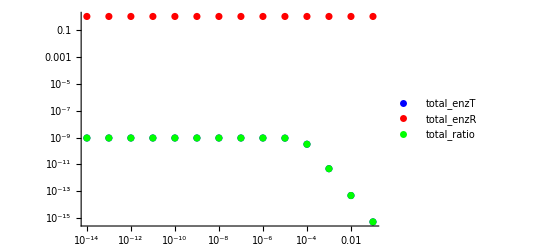

```mathematica
enzTPlot = ListLogLogPlot[Tooltip@Map[{ 10.^#,allEnzT/.fdp^c-> 10^#}&,Range[-14,-1]], PlotStyle-> Blue, PlotLegends-> {"total_enzT"}];
enzRPlot= ListLogLogPlot[Tooltip@Map[{ 10.^#,allEnzR/.fdp^c-> 10^#}&,Range[-14,-1]], PlotStyle->Red, PlotLegends-> {"total_enzR"}];
enzRatioPlot = ListLogLogPlot[Tooltip@Map[{ 10.^#,enzRatio/.fdp^c-> 10^#}&,Range[-14,-1]], PlotStyle->Green, PlotLegends-> {"total_ratio"}];
Show[{enzTPlot,enzRPlot,enzRatioPlot}, PlotRange-> All]
```

#### Get free T/R ratio

```mathematica
enzT = Values@FilterRules[enzSolSub,(FBP2T^c)_^];
enzT = Simplify[enzT/.ratesSub/.paramFitSub/.reverseZeroSub/.enzymeSub][[1]];
Map[{ 10.^#,enzT/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,9.25722×10^-10},{1.×10^-13,9.25722×10^-10},{1.×10^-12,9.25722×10^-10},{1.×10^-11,9.25722×10^-10},{1.×10^-10,9.25722×10^-10},{1.×10^-9,9.25722×10^-10},{1.×10^-8,9.25722×10^-10},{1.×10^-7,9.2572×10^-10},{1.×10^-6,9.25544×10^-10},{0.00001,9.0839×10^-10},{0.0001,3.18528×10^-10},{0.001,4.83599×10^-12},{0.01,4.90868×10^-14},{0.1,5.38411×10^-16}}

```mathematica
enzR = Values@FilterRules[enzSolSub,(FBP2R^c)_^];
enzR = Simplify[enzR/.ratesSub/.paramFitSub/.reverseZeroSub/.enzymeSub][[1]];
Map[{ 10.^#,enzR/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,1.},{1.×10^-13,1.},{1.×10^-12,1.},{1.×10^-11,1.},{1.×10^-10,1.},{1.×10^-9,1.},{1.×10^-8,1.},{1.×10^-7,0.999998},{1.×10^-6,0.999808},{0.00001,0.981277},{0.0001,0.344086},{0.001,0.00522402},{0.01,0.0000530254},{0.1,5.81612×10^-7}}

```mathematica
enzRatio=Values@FilterRules[enzSolSub,(FBP2T^c)_^]/Values@FilterRules[enzSolSub,(FBP2R^c)_^];
enzRatio = enzRatio/.ratesSub/.paramFitSub/.reverseZeroSub/.enzymeSub;
enzRatio =Simplify[enzRatio, TimeConstraint->{30,300}][[1]];
Map[{ 10.^#,enzRatio/.fdp^c-> 10^#}&,Range[-14,-1]]
```

{{1.×10^-14,9.25722×10^-10},{1.×10^-13,9.25722×10^-10},{1.×10^-12,9.25722×10^-10},{1.×10^-11,9.25722×10^-10},{1.×10^-10,9.25722×10^-10},{1.×10^-9,9.25722×10^-10},{1.×10^-8,9.25722×10^-10},{1.×10^-7,9.25722×10^-10},{1.×10^-6,9.25722×10^-10},{0.00001,9.25722×10^-10},{0.0001,9.25722×10^-10},{0.001,9.25722×10^-10},{0.01,9.25722×10^-10},{0.1,9.25722×10^-10}}

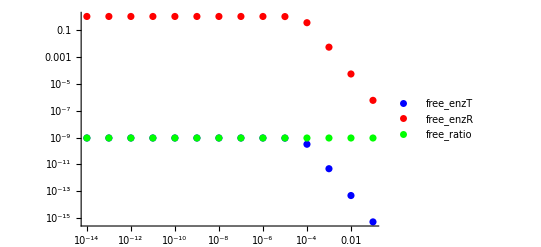

```mathematica
enzTPlot = ListLogLogPlot[Tooltip@Map[{ 10.^#,enzT/.fdp^c-> 10^#}&,Range[-14,-1]], PlotStyle-> Blue, PlotLegends-> {"free_enzT"}];
enzRPlot= ListLogLogPlot[Tooltip@Map[{ 10.^#,enzR/.fdp^c-> 10^#}&,Range[-14,-1]], PlotStyle->Red, PlotLegends-> {"free_enzR"}];
enzRatioPlot = ListLogLogPlot[Tooltip@Map[{ 10.^#,enzRatio/.fdp^c-> 10^#}&,Range[-14,-1]], PlotStyle->Green, PlotLegends-> {"free_ratio"}];
Show[{enzTPlot,enzRPlot,enzRatioPlot}, PlotRange-> All]
```

```mathematica
NullSpace@enzymeModelOrig["Stoichiometry"]
```

{}

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
dataHeader = Import[dataFilePath][[1]];
```

```mathematica
backCalculateKms[rxn, s05List,relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00363 | 0.00389758 | 7.37123

```mathematica
backCalculateHillCoef[fittingData, filteredDataList[[paramSet]],dataHeader, s05List, otherParmsList]//TableForm
```

data value | predicted value | error in %
3.2 | 2.1187 | 33.7905

```mathematica
backCalculateKcats[rxn, kcatList,absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
369.346 | 309.989 | 16.0708

```mathematica
backCalculateRatios[haldaneRatiosList,{KeqList[[All,3]]},  paramFitSub]//TableForm
```

data value | predicted value | error in %
22000 | 22000. | 5.70516×10^-6

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

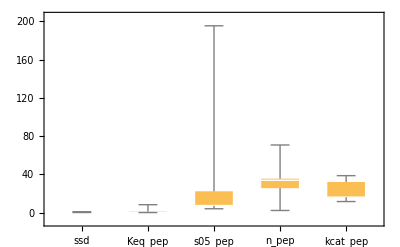

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
Dimensions@predictedParameterErrors[[3;;]]
```

{100,5}

```mathematica
predictedParameterErrors[[3;;]]//TableForm
```

0.00325662 | 0.0806575 | 3.12273 | 5.82114 | 5.18381
0.00326089 | 0.00654823 | 3.09714 | 5.92629 | 5.22879
0.00331574 | 0.71387 | 3.04102 | 5.54487 | 5.09685
0.00445043 | 0.608439 | 3.76164 | 7.33124 | 5.70839
0.00520588 | 1.29219 | 3.95771 | 8.03482 | 6.04657
0.00726106 | 1.72162 | 4.6583 | 8.84744 | 6.29259
0.048924 | 1.11618 | 11.5652 | 11.2082 | 7.31091
1.84351 | 1.65179 | 99.6863 | 53.7694 | 34.4697
1.84717 | 3.67043 | 101.121 | 54.0056 | 34.8266
10.1265 | 8.70468 | 645.184 | 83.4741 | 92.2344

```mathematica
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]]
```

```mathematica
paramFitSub
```

{k_PYK11^⟵→17878.6,k_PYK11^⟶→7.64722×10^7,k_PYK110^⟵→9.82673×10^8,k_PYK110^⟶→2452.32,k_PYK111^⟵→0.386065,k_PYK111^⟶→3.38409×10^6,k_PYK112^⟵→9.94914×10^8,k_PYK112^⟶→2402.95,k_PYK113^⟵→0.481284,k_PYK113^⟶→3.51373×10^7,k_PYK114^⟵→2.43127×10^8,k_PYK114^⟶→9465.43,k_PYK115^⟵→454.351,k_PYK115^⟶→8.21788×10^6,k_PYK116^⟵→1.42479×10^6,k_PYK116^⟶→4058.36,k_PYK117^⟵→184.227,k_PYK117^⟶→2691.65,k_PYK12^⟵→1.73235×10^6,k_PYK12^⟶→2441.71,k_PYK13^⟵→1.03191×10^7,k_PYK13^⟶→3.50271×10^7,k_PYK14^⟵→1.×10^9,k_PYK14^⟶→8996.54,k_PYK15^⟵→1.48807×10^7,k_PYK15^⟶→6.64247×10^8,k_PYK16^⟵→4743.15,k_PYK16^⟶→74768.6,k_PYK17^⟵→2.11085×10^6,k_PYK17^⟶→4.29291×10^8,k_PYK18^⟵→9.67107×10^8,k_PYK18^⟶→2687.8,k_PYK19^⟵→53.9007,k_PYK19^⟶→1.43155×10^8}

```mathematica
data =Table[
MapThread [#2/#1&,{filteredDataList[[paramSetI,2]][[1;;-1;;2]],filteredDataList[[paramSetI,2]][[2;;-1;;2]]}],
{paramSetI, 1, numFits }];
```

```mathematica
MapThread[{parameter["K"<>ToString[#3]], #2/#1}&,{filteredDataList[[paramSet,2]][[1;;-1;;2]],filteredDataList[[paramSet,2]][[2;;-1;;2]],Range[Length@filteredDataList[[paramSet,2]][[1;;-1;;2]]]}]
```

{{K1_Global,4277.29},{K2_Global,2.49556×10^-6},{K3_Global,8.76559×10^6},{K4_Global,2.41523×10^-6},{K5_Global,7.30075×10^7},{K6_Global,0.0000389321},{K7_Global,18087.1},{K8_Global,0.0028484},{K9_Global,14.6105},{K10_Global,0.00140948},{K11_Global,3.3944},{K12_Global,8.99654×10^-6},{K13_Global,44.6382},{K14_Global,15.7635},{K15_Global,203.374},{K16_Global,2.77922×10^-6},{K17_Global,2.6559×10^6}}

```mathematica
data//TableForm
```

4277.29 | 2.49556×10^-6 | 8.76559×10^6 | 2.41523×10^-6 | 7.30075×10^7 | 0.0000389321 | 18087.1 | 0.0028484 | 14.6105 | 0.00140948 | 3.3944 | 8.99654×10^-6 | 44.6382 | 15.7635 | 203.374 | 2.77922×10^-6 | 2.6559×10^6
4296.83 | 0.0000181732 | 223611. | 0.0000306705 | 12091.7 | 6.53577×10^-6 | 89.128 | 0.0000319468 | 2.85987×10^10 | 1.52878×10^-6 | 2.49004 | 657829. | 127.805 | 5.51353×10^-6 | 3913.3 | 3.57209×10^-6 | 258.774
4302.46 | 0.0000318103 | 2.00417 | 6.2483×10^-6 | 6.03348×10^6 | 4.13589×10^-6 | 11464.6 | 2.66076×10^-6 | 2.38953 | 0.0000772 | 2.87547 | 0.529135 | 36.291 | 0.00144446 | 17931.9 | 0.269112 | 2.35809×10^11
4008.07 | 3.67572×10^-6 | 629416. | 0.0000282754 | 2278.71 | 3.92408×10^6 | 12507.1 | 0.0000681998 | 0.151136 | 0.0000117457 | 8.62123 | 5.37646×10^-6 | 2.69506 | 8.81321 | 262775. | 0.000012269 | 1735.3
2.87481 | 4.42618×10^-6 | 3.40154×10^14 | 5.71968×10^-6 | 4319.97 | 5.24074×10^-6 | 2757.81 | 0.98302 | 8.38764×10^-6 | 29.2235 | 420.815 | 0.0000332675 | 4531.29 | 0.0000520904 | 7.78207×10^8 | 0.0000136693 | 1.65877
10.4053 | 4.92604×10^-6 | 1.90919 | 0.0160041 | 64191. | 2.3884×10^-6 | 5.54795×10^12 | 0.0000179246 | 1.4847×10^6 | 0.00037828 | 88.2285 | 3.93462×10^-6 | 1023.81 | 0.000379159 | 360.059 | 0.0000785673 | 422926.
1.26073×10^13 | 2.27912×10^-6 | 66.3076 | 0.617743 | 707508. | 1.50397×10^-6 | 684.529 | 0.000012274 | 1.85708×10^7 | 0.000237262 | 5.50494 | 4.56958×10^-6 | 167.157 | 4.00202×10^-6 | 4126.82 | 3.4751×10^-6 | 1944.31
0.210515 | 0.0000118269 | 840083. | 0.131374 | 0.93146 | 0.0000428283 | 9.3064×10^7 | 4.68379×10^-6 | 0.606558 | 3.6916×10^-6 | 2.70583×10^6 | 0.000197272 | 6.25424×10^13 | 4.49939×10^-6 | 1829.97 | 2.13399×10^-6 | 3563.35
1.33662×10^9 | 3.92976×10^-6 | 721.869 | 3.93654×10^-6 | 842.663 | 23853.5 | 2046.13 | 0.0000186004 | 0.335536 | 3.93575×10^-6 | 1.28886×10^9 | 3.93428×10^-6 | 0.199178 | 3.93501×10^-6 | 2.39367×10^8 | 3.93735×10^-6 | 375.214
402.366 | 0.961945 | 1.82341×10^7 | 9.4041×10^-7 | 0.999197 | 5.65078×10^8 | 216608. | 4.70179×10^-6 | 1.62296×10^9 | 1.01374×10^-6 | 1088.56 | 1.18044×10^-6 | 2407.18 | 9.69931×10^-7 | 1.13169 | 9.72238×10^-7 | 1.15378

```mathematica
tickLabels = MapThread[{#1, Rotate[#2, 90 Degree]}&,{Range[17],enzymeModelOrig["Reactions"]}];
```

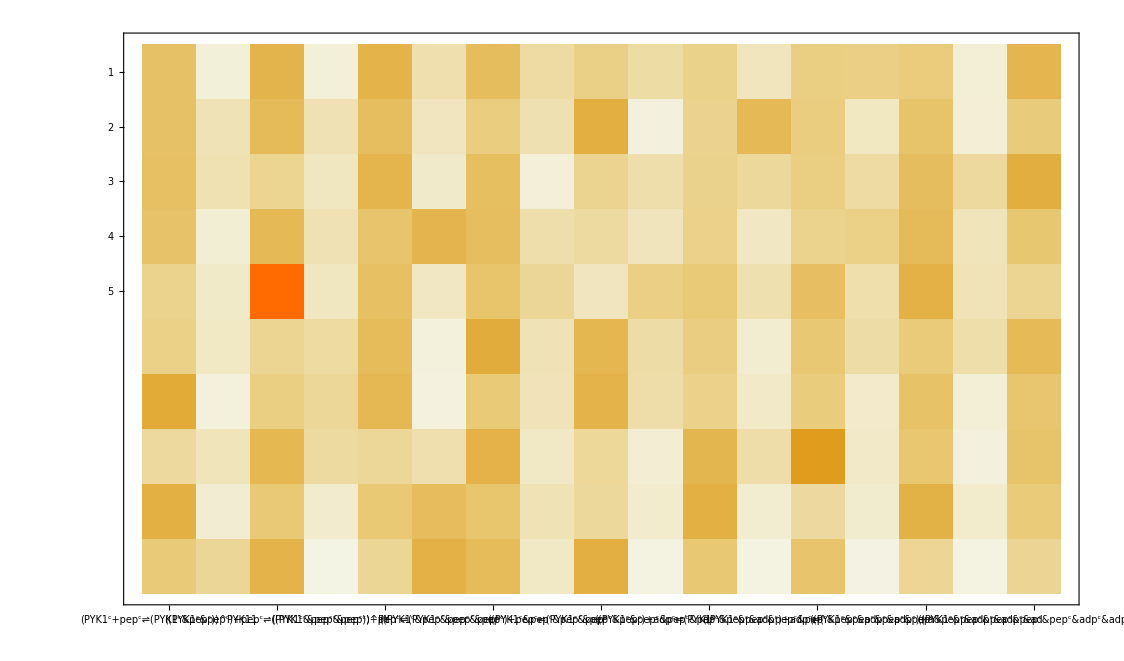

```mathematica
MatrixPlot[data,FrameTicks->{{1,2,3, 4,5},tickLabels}]
```

```mathematica
enzymeModelOrig["Reactions"]
```

{((PYK1^c)_^+pep^c⇌(PYK1^c&pep^c)_^)^PYK11,((PYK1^c&pyr^c)_^⇌(PYK1^c)_^+pyr^c)^PYK12,((PYK1^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c)_^)^PYK13,((PYK1^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c)_^+pyr^c)^PYK14,((PYK1^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c)_^)^PYK15,((PYK1^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c)_^+pyr^c)^PYK16,((PYK1^c&pep^c&pep^c&pep^c)_^+pep^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c)_^)^PYK17,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c)_^+pyr^c)^PYK18,((PYK1^c&pep^c&pep^c&pep^c&pep^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^)^PYK19,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c)_^+atp^c)^PYK110,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^)^PYK111,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c)_^+atp^c)^PYK112,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^)^PYK113,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c)_^+atp^c)^PYK114,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c)_^+adp^c⇌(PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^)^PYK115,((PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c)_^+atp^c)^PYK116,((PYK1^c&pep^c&pep^c&pep^c&pep^c&adp^c&adp^c&adp^c&adp^c)_^⇌(PYK1^c&pyr^c&pyr^c&pyr^c&pyr^c&atp^c&atp^c&atp^c&atp^c)_^)^PYK117}